```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.1*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[4]={1,4,2,1}; s[3]={2,1,3,2}; s[2]={3,2,4,3}; s[1]={4,1,3,4};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,0,1,2},{0,1,2,1},{1,2,1,0},{2,1,0,1}}

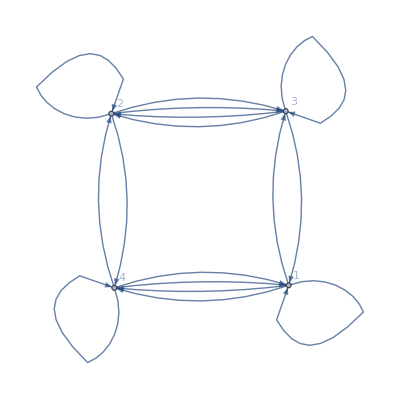

```mathematica
AdjacencyGraph[M,DirectedEdges->True,VertexLabels->"Name"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

16 x-4 x^2-4 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→-2.},{x→0.+0. ⅈ},{x→2.},{x→4.}}

```mathematica
r[i_]:={Re[x],Im[x]}/.NSolve[Det[M-x*IdentityMatrix[n0]]==0,x][[i]]
```

```mathematica
Clear[s]
```

```mathematica
s[4]={1,4,2,1}; s[3]={2,1,3,2}; s[2]={3,2,4,3}; s[1]={4,1,3,4};
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{4,1,3,4,3,2,4,3,2,1,3,2,1,4,2,1}

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[7];
```

```mathematica
Length[aa]
```

65536

```mathematica
bb=aa/. 1->{1.0,0,0} /. 2->N[{-1/2,Sqrt[3]/2,0} ]/. 3->N[{-1/2,-Sqrt[3]/2,0}]/. 4->{0,0,1.0} ;
```

```mathematica
cc=FoldList[Plus,{0,0,0},N[bb]];
```

```mathematica
g1=ListPointPlot3D[cc,PlotRange->All,ColorFunction->Hue,Axes->False,ImageSize->Full,PlotStyle->PointSize[0.001]];
```

```mathematica
g2=Show[g1,ViewPoint->Above];
```

```mathematica
g3=Show[g1,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g1,ViewPoint->Right];
```

```mathematica
Export["Triagle_Carpet_substitution_Level7_grid.jpg" ,GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->{{4000,4000}}]]
```

```mathematica
(*end*)
```